```mathematica
Work[n_]:=Block[{i, currentGraph,contract, graphs=Association[],deps={}, nodeCount=VertexCount[ReadGrof[2]],next=Association[],added},
graphs[1]=ReadGrof[1];
Monitor[
For[i=2,i<=n,i++,
currentGraph=ReadGrof[i];
added=False;
If[VertexCount[currentGraph]≠nodeCount,
Print[{i,VertexCount[currentGraph]}];
graphs=next;
next=Association[];
nodeCount=VertexCount[currentGraph]
];
next[i]=currentGraph;
Table[
contract=EdgeContract[currentGraph,e];
Table[
(*Print[{i,j},e,IsomorphicGraphQ[contract,graphs[j]],Graph[contract,VertexLabels->"Name",GraphLayout->"PlanarEmbedding"],Graph[graphs[j],VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]];*)
If[IsomorphicGraphQ[contract,graphs[j]],
AppendTo[deps,i->j];
added=True
];
,{j, Keys[graphs]}
]
,
{e,CollectMPGEdges[currentGraph]}
];
If[!added,Print[i]]
],
{i,n}
];
DeleteDuplicates[deps]
]
```

```mathematica
labels=Table[k->ChromaticPolynomial[ReadGrof[k],4]/24,{k,50}];
```

```mathematica
CollectMPGEdges[ReadGrof[2]]
```

{1<->2,1<->3,1<->5,2<->4,3<->4,4<->5}

```mathematica
Table[{e,IsomorphicGraphQ[EdgeContract[ReadGrof[2],e],ReadGrof[1]]},{e,CollectMPGEdges[ReadGrof[2]]}]
```

{{1<->2,True},{1<->3,True},{1<->5,True},{2<->4,True},{3<->4,True},{4<->5,True}}

{3,6}

{5,7}

{10,8}

{24,9}

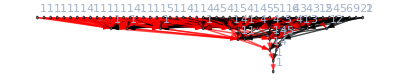

```mathematica
With[
{max=73},
With[{edges=Work[max],grofs=Table[ChromaticPolynomial[ReadGrof[k],4]/24,{k,max}]},
Graph[
edges,
GraphLayout->"LayeredDigraphEmbedding",
EdgeStyle->Table[e->If[grofs[[e[[1]]]]==grofs[[e[[2]]]],Red,Black],{e,edges}],
VertexLabels->Table[k->grofs[[k]],{k,max}]]
]
]
```

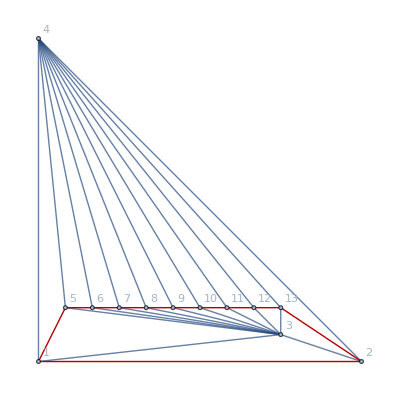

```mathematica
With[{max=9},
With[{h=JacobsThalGraph[max],g=JacobsThalGraph[max-1]},
{Graph[h,
VertexLabels->"Name",
GraphLayout->"PlanarEmbedding",
GraphHighlight->Map[First,Select[Table[{e,IsomorphicGraphQ[EdgeContract[h,e],g]},{e,CollectMPGEdges[h]}],#[[2]]&]],
GraphHighlightStyle->"Thick",
ImageSize->400
]}
]
]
```